Wolfram Online Mini Campus. Part 7

Instagram Posts
Pinterest Posts
"Translation" of  SageMath Online Mini Campus. Part 7

Matrix Forms as PlayGrounds

((A_11 | A_12
A_21 | A_22) | (B_11 | B_12
B_21 | B_22)
(C_11 | C_12
C_21 | C_22) | (D_11 | D_12
D_21 | D_22))

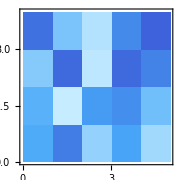

(2.3×10^-4 | 9.1×10^-4 | 1.2×10^-3 | 4.×10^-4 | 1.5×10^-4
9.4×10^-4 | 2.×10^-4 | 1.23×10^-3 | 2.×10^-4 | 3.7×10^-4
7.×10^-4 | 1.25×10^-3 | 5.2×10^-4 | 4.1×10^-4 | 8.6×10^-4
6.4×10^-4 | 3.3×10^-4 | 1.02×10^-3 | 5.9×10^-4 | 1.09×10^-3)

{(23 | 91 | 120 | 40 | 15
94 | 20 | 123 | 20 | 37
70 | 125 | 52 | 41 | 86
64 | 33 | 102 | 59 | 109)→(10111_2 | 1011011_2 | 1111000_2 | 101000_2 | 1111_2
1011110_2 | 10100_2 | 1111011_2 | 10100_2 | 100101_2
1000110_2 | 1111101_2 | 110100_2 | 101001_2 | 1010110_2
1000000_2 | 100001_2 | 1100110_2 | 111011_2 | 1101101_2)→(000010111_2 | 001011011_2 | 001111000_2 | 000101000_2 | 000001111_2
001011110_2 | 000010100_2 | 001111011_2 | 000010100_2 | 000100101_2
001000110_2 | 001111101_2 | 000110100_2 | 000101001_2 | 001010110_2
001000000_2 | 000100001_2 | 001100110_2 | 000111011_2 | 001101101_2)}

```mathematica
Manipulate[Style[MatrixForm[Array[Subscript[α,##] &,
{N,N}]],{Medium,Bold,c}],
{N,Range[2,5,1]},{c,{Darker[Gray],Blue,Orange}}]
MatrixForm[Partition[Map[{{Subscript[#,11],
Subscript[#,12]},{Subscript[#,21],
Subscript[#,22]}}&,{A,B,C,D}],2]]
m=RandomInteger[{0,127},{4,5}]; mf=MatrixForm[m];
MatrixPlot[m,ColorFunction->"DeepSeaColors",
ImageSize->Small]
ScientificForm[MatrixForm[m/10.^5]]
{mf->BaseForm[mf,2]->PaddedForm[BaseForm[mf,2],
8,NumberPadding -> {"0", ""}]}
```

Surfaces as PlayGrounds

```mathematica
h=x^4+y^4+z-3; g=x^3+y^2-z^3;
ContourPlot3D[{h==0,g==0},
{x,-2,2},{y,-2,2}, {z,-2,2},
MeshFunctions->{Function[{x,y,z,f},h-g]},
MeshStyle->{{Thick,Blue}}, Mesh->{{0}},
ContourStyle ->Opacity[0.5],ImageSize->Medium,
ColorFunction->"DeepSeaColors",
Boxed->False,Axes->False,
PlotLabel->"Surfaces' Intersection"]
```

-Graphics3D-

```mathematica
cp1=ContourPlot3D[z==x^4+y^3-1,
{x,-2,2},{y,-2,2},{z,-1,1},
ContourStyle->{Blue,Opacity[0.2]},
Mesh->20,MeshStyle->{Darker[Blue],Blue},
MeshFunctions->{Sin[2#1*#3]&,Cos[3#2*#3]&}];
cp2=Graphics3D[{Opacity[.5],EdgeForm[Darker[Blue]],
Translate[Icosahedron[0.3],
Table[{x,(1-x^4)^(1/3),0},{x,Range[-1,1,0.5]}]]}];
Show[cp1,cp2,PlotRange->All,Axes->False,
Boxed->False,PlotLabel->"Surfaces' Translation"]
```

-Graphics3D-

```mathematica
Plot3D[Table[(x^2-y^2)^4 *z^2,{z,9,49,10}] // Evaluate,
{x,-.5,.5},{y,-.5,.5}, PlotStyle->Opacity[.3],
ColorFunction->"BrightBands",Mesh->False,
ClippingStyle->None,Boxed->False,
Axes->False,PlotLabel->"Surfaces' Coordinates"]
```

-Graphics3D-

Lists & Arrays as PlayGrounds

{{33/16,25/16,3/2,25/16,33/16,5/2},{41/16,33/16,2,33/16,41/16,3},{33/16,25/16,3/2,25/16,33/16,5/2},{25/16,17/16,1,17/16,25/16,2}}

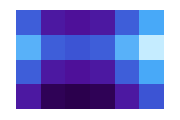

{{0.1,0.05,0.95},{0.09,0.03,0.08},{0.01,0.09,0.91},{0.04,0.92,0.07},{0.05,0.02,0.04}}

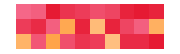

{{1},{0},{1},{2},{0},{2},{1},{0},{1},{2}}

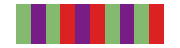

```mathematica
A=Array[1+Sin[#1Pi/4]^2+Cos[#2Pi/6]^4 &,{4,6}]
ArrayPlot[A,ColorFunction->"DeepSeaColors",ImageSize->Small]
X={{.10,.05,.95},{.09,.03,.08},{.01,.09,.91},{.04,.92,.07},{.05,.02,.04},
      { .07,.97,.05},{.06,.02,.98},{.02,.06,.03},{.01,.09,.03},{.02,.94,.01}};
X[[1;;5]]      
ArrayPlot[Transpose[X],ColorFunction->"BrightBands",ImageSize->Small]
Y=Transpose[{{1,0,1,2,0,2,1,0,1,2}}]
ArrayPlot[Transpose[Y],ColorFunction->"Rainbow",ImageSize->Small]
```

Sigmoid Activation

```mathematica
synapse0=RandomVariate[NormalDistribution[0,1],3]
sigmoid[x_]=1.0/(1+Exp[-x]); sigmoidderivation[x_]=x*(1.0-x);
sigmoid/@X==sigmoid[X]
Do[{layer0=X;layer1=sigmoid[Dot[layer0,synapse0]];
layer1error=layer1-Y;
layer1delta=layer1error*sigmoidderivation[layer1]; 
synapse0derivative=Dot[Transpose[layer0],layer1delta]; 
synapse0=synapse0-synapse0derivative},{i,100}]
TableForm[{X,layer1,Y}]
```

{0.43625,1.07933,0.58875}

True

0.1
0.05
0.95 | 0.09
0.03
0.08 | 0.01
0.09
0.91 | 0.04
0.92
0.07 | 0.05
0.02
0.04 | 0.07
0.97
0.05 | 0.06
0.02
0.98 | 0.02
0.06
0.03 | 0.01
0.09
0.03 | 0.02
0.94
0.01
0.911073 | 0.559246 | 0.928788 | 0.994569 | 0.53509 | 0.995524 | 0.907086 | 0.593028 | 0.635328 | 0.99456
1 | 0 | 1 | 2 | 0 | 2 | 1 | 0 | 1 | 2

Complex Numbers as PlayGrounds

{1+4 ⅈ,2-3 ⅈ,3+ⅈ,-1+7 ⅈ,14+5 ⅈ,-10/13+(11 ⅈ)/13,-15+8 ⅈ,1.45186-0.493404 ⅈ}

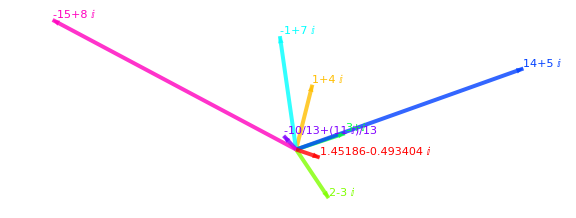

```mathematica
z1=1+4*I; z2=2-3*I; 
Z={z1,z2,z1+z2,z1-z2,z1*z2,z1/z2,z1^2,N[z2^(1/3)]}
tc=Table[Graphics[{Hue[i/8],Thickness[0.005],
Opacity[0.8],Arrowheads[0.04],
Arrow[{{0,0},ReIm[Z[[i]]]}]}],{i,8}];
tx=Table[Graphics[{Text[Style[Z[[i]],
Hue[i/8],FontSize->Medium],
ReIm[Z[[i]]],{-1,-1}]}],{i,8}];
Show[tc,tx,ImageSize->Large]
```

```mathematica
z1=1+5*I; z2=4-3*I;
ParametricPlot[{ReIm[(z1)^x/5],ReIm[(z2)^x/5],
ReIm[(z1+z2)^x/5],ReIm[(z1-z2)^x],
ReIm[(z1*z2)^(x/10)],ReIm[(z1/z2)^(10x)]},
{x,-10,10},PlotStyle->"BrightBands",PlotTheme->"Detailed",
PlotRange->{{-10,10},{-10,10}},PlotLegends->"Expressions"]
```

-Graphics-

```mathematica
ReImPlot[{ArcSin[(2-5*I)^x], ArcCos[(2-5*I)^x]},
{x,-5,5},ColorFunction->Hue,PlotStyle->Thickness[0.01],
ImageSize->700,PlotLabels -> "Expressions",
GridLines->Automatic]
```

-Graphics-